```mathematica
Solve[a==a/(1-a*b)&&b==0.25,{a}]
```

{}

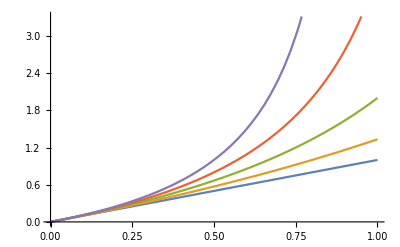

```mathematica
Plot[Evaluate@Table[a/(1-a*b)/.b->bb,{bb,0,1,0.25}],{a,0,1}]
```

Power::infy: Infinite expression 1/0. encountered.

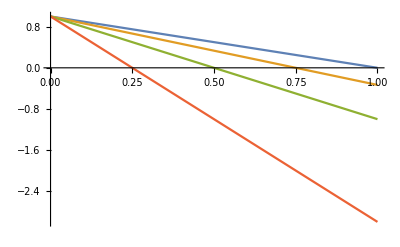

```mathematica
Plot[Evaluate@Table[(1-b-a)/(1-b)/.b->bb,{bb,0,1,0.25}],{a,0,1}]
```

```mathematica
f[a_,b_]:=a/(1-a*b)
f[]
```

f[]

```mathematica
For[t=0.25;k=1,k≤10000,k++,t=(t/(1-t*0.9))*2];Print[t]
```

-1.11111

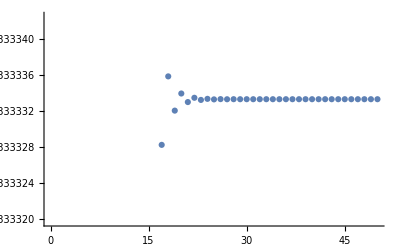

```mathematica
initialCfp=0.02;cv=0.5;
conc={};For[cfp=0.02;i=1,i≤50,i++,cfp=initialCfp-cv*cfp;AppendTo[conc,cfp]]
ListPlot@conc
```

```mathematica
;
```

```mathematica
initialCfp=0.02;cv=0.01;
conc={};For[cfp=0.02;i=1,i≤500,i++,cfp=initialCfp-cv*cfp];AppendTo[conc,cfp]
```

{0.019802}

```mathematica
conc={};Table[For[cfp=0.02;i=1,i≤500,i++,cfp=k-cv*cfp];AppendTo[conc,cfp],{k,0.001,0.02,0.001}][[-1]]
```

{0.000990099,0.0019802,0.0029703,0.0039604,0.0049505,0.00594059,0.00693069,0.00792079,0.00891089,0.00990099,0.0108911,0.0118812,0.0128713,0.0138614,0.0148515,0.0158416,0.0168317,0.0178218,0.0188119,0.019802}

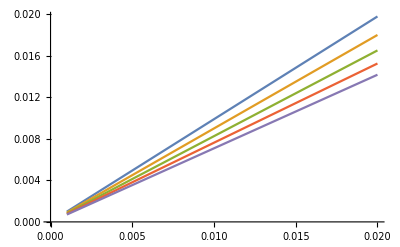

```mathematica
data=Table[Table[conc={};{k,For[cfp=0.02;i=1,i≤500,i++,cfp=k-j*cfp];AppendTo[conc,cfp][[1]]},{k,0.001,0.02,0.001}],{j,0.01,0.5,0.1}];
ListLinePlot@data
```

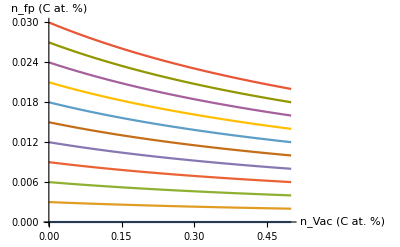

```mathematica
data=Table[Table[conc={};{j,For[cfp=0.02;i=1,i≤500,i++,cfp=k-j*cfp];AppendTo[conc,cfp][[1]]},{j,0.00,0.5,0.02}],{k,0.00,0.03,0.003}];
ListLinePlot[data,AxesLabel->{"n_Vac (C at. %)","n_fp (C at. %)"}]
```

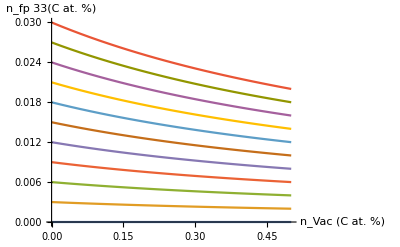

```mathematica
data=Table[Table[conc={};{j,For[cfp=0.02;i=1,i≤500,i++,cfp=k-j*cfp];AppendTo[conc,cfp][[1]]},{j,0.00,0.5,0.02}],{k,0.00,0.03,0.003}];
ListLinePlot[data,AxesLabel->{"n_Vac (C at. %)","n_fp 33(C at. %)"}]
```

```mathematica
plotOptions={AspectRatio->0.66,FrameLabel->{Style["n_vac (at. %) ",20,Black],Style["n_fp (at. %)",20,Black]},FrameTicksStyle->Directive[20,Black],Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],ImageSize->470,PlotRange->{Automatic,{1.3,3.3}},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007],Black,Dashing[0.03]],ImageSize->6000,PlotLegends->Placed[{Style["Bound",18]},{0.83,0.93}]};
plotOptions2={AspectRatio->0.66,FrameLabel->{Style["n_vac (at. %) ",20,Black],Style["n_fp (at. %)",20,Black]},FrameTicksStyle->Directive[20,Black],Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],ImageSize->470,PlotRange->{Automatic,Automatic},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007],Red],ImageSize->600,PlotLegends->Placed[{Style["Unbound",18]},{0.83,0.83}]};
```

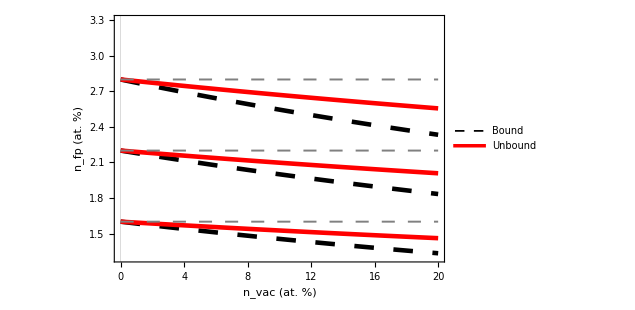

```mathematica
p1=Plot[{Evaluate@Table[100*i/(1+x/100),{i,0.01,0.03,0.006}]},{x,0,20},Evaluate@plotOptions];
p2=Plot[{Evaluate@Table[100*i/(1+x/100)^0.5,{i,0.01,0.03,0.006}]},{x,0,20},Evaluate@plotOptions2];
p3=Plot[{Table[100*i,{i,0.01,0.03,0.006}]},{x,0,20},PlotStyle->Directive[Gray,Dashing[0.02],Thickness[0.003]]];
frenkvsvac=Show[{p1,p2,p3}]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Notes-post-doc/images/frenkel-conc-vs-vac-conc.pdf",frenkvsvac]
```

/Users/tom/Documents/Lyx_documents/Notes-post-doc/images/frenkel-conc-vs-vac-conc.pdf

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

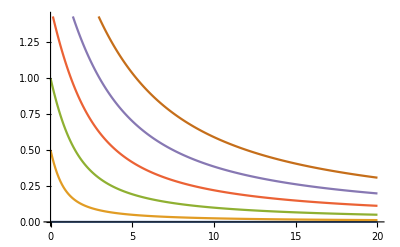

```mathematica
dataQ4=Table[Table[{100*n0,100*(nfp/.Solve[nfp0^2/(nfp+n0)==nfp,{nfp}][[2]])},{n0,0.00,0.2,0.001}],{nfp0,0.00000001,0.03,0.005}];
ListLinePlot[dataQ4]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

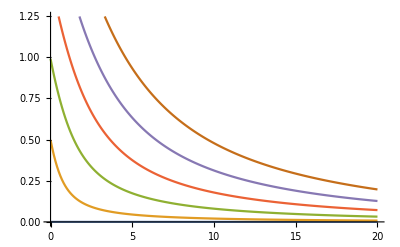

```mathematica
dataQ5=Table[Table[{100*n0,100*(nfp/.Solve[(1-n0-nfp)^2*(nfp0^2)/(nfp+n0)==nfp,{nfp}][[2]])},{n0,0.00,0.2,0.001}],{nfp0,0.00000001,0.03,0.005}];
ListLinePlot[dataQ5]
```

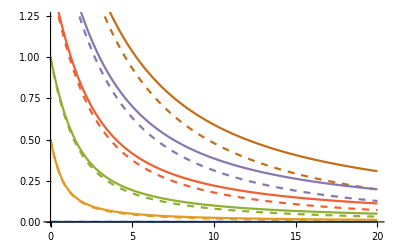

```mathematica
Show[ListLinePlot[dataQ5,PlotStyle->Dashed],ListLinePlot[dataQ4]]
```

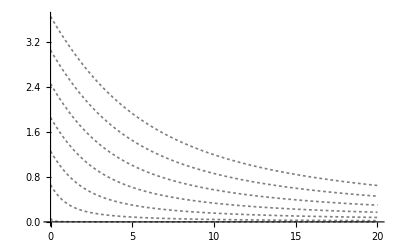

```mathematica
ListLinePlot[dataQ4,PlotStyle->Directive[Gray,Dashing[0.005],Thickness[0.003]]]
```

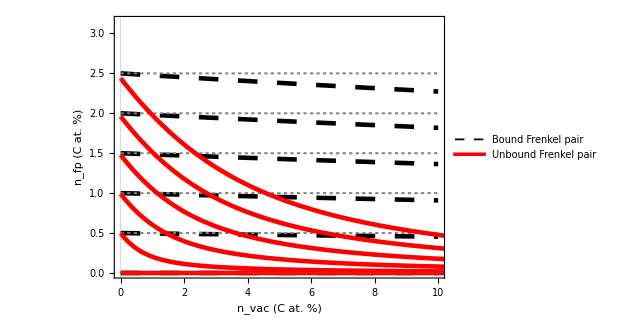

```mathematica
plotOptions3={AspectRatio->0.7,FrameLabel->{Style["n_vac (C at. %) ",20,Black],Style["n_fp (C at. %)",20,Black]},FrameTicksStyle->Directive[20,Black],Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],ImageSize->470,PlotRange->{Automatic,{0.0,3.15}},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007],Black,Dashing[0.03]],ImageSize->6000,PlotLegends->Placed[{Style["Bound Frenkel pair",18]},{0.71,0.93}]};
plotOptions4={AspectRatio->0.7,FrameLabel->{Style["n_vac (C at. %) ",20,Black],Style["n_fp (C at. %)",20,Black]},FrameTicksStyle->Directive[20,Black],Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],ImageSize->470,PlotRange->{Automatic,Automatic},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007],Red],ImageSize->600,PlotLegends->Placed[{Style["Unbound Frenkel pair",18]},{0.71,0.83}]};

q1=Plot[{Evaluate@Table[100*i/(1+x/100),{i,0.000,0.029,0.005}]},{x,0,10},Evaluate@plotOptions3];
q2=Plot[{Evaluate@Table[100*i/(1+x/100)^0.5,{i,0.000,0.029,0.005}]},{x,0,10},Evaluate@plotOptions4];
q3=Plot[{Table[100*i,{i,0.000,0.029,0.005}]},{x,0,10},PlotStyle->Directive[Gray,Dashing[0.005],Thickness[0.003]]];
q4=ListLinePlot[dataQ4[[1;;-1]],PlotRange->All,Evaluate@plotOptions4];
q5=ListLinePlot[dataQ5[[1;;-1]],PlotRange->All,Evaluate@plotOptions4];
frenkvsvac2=Show[{q1,q3,q5}]
```

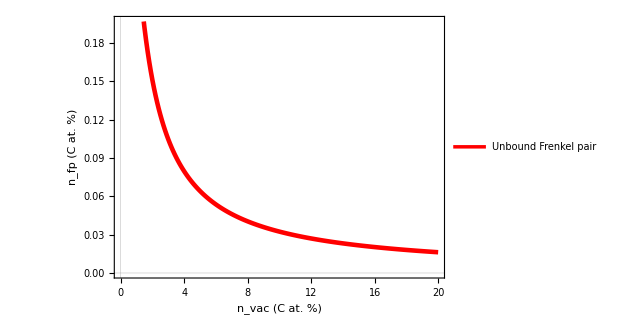

```mathematica
q4=ListLinePlot[dataQ4[[2]],Evaluate@plotOptions4]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/frenkel-conc-vs-vac-conc.pdf",frenkvsvac2]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/frenkel-conc-vs-vac-conc.pdf

```mathematica
dataQ5=Table[Table[{100*n0,100*(nfp/.Solve[(1-n0-nfp)^2*(nfp0^2)/(nfp+n0)==nfp,{nfp}][[2]])},{n0,0.00,0.2,0.001}],{nfp0,0.00000001,0.03,0.005}];
ListLinePlot[dataQ5]
```

```mathematica
onePercentScale=With[{n0=0.01},Table[{100*nfp0,100*(nfp/.Solve[(1-n0-nfp)^2*(nfp0^2)/(nfp+n0)==nfp,{nfp}][[2]])},{nfp0,0.0000001,0.02,0.001}]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
twoPercentScale=With[{n0=0.02},Table[{100*nfp0,100*(nfp/.Solve[(1-n0-nfp)^2*(nfp0^2)/(nfp+n0)==nfp,{nfp}][[2]])},{nfp0,0.0000001,0.02,0.00001}]];
```

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
threePercentScale=With[{n0=0.03},Table[{100*nfp0,100*(nfp/.Solve[(1-n0-nfp)^2*(nfp0^2)/(nfp+n0)==nfp,{nfp}][[2]])},{nfp0,0.0000001,0.02,0.001}]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
fourPercentScale=With[{n0=0.04},Table[{100*nfp0,100*(nfp/.Solve[(1-n0-nfp)^2*(nfp0^2)/(nfp+n0)==nfp,{nfp}][[2]])},{nfp0,0.0000001,0.02,0.001}]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
fivePercentScale=With[{n0=0.05},Table[{100*nfp0,100*(nfp/.Solve[(1-n0-nfp)^2*(nfp0^2)/(nfp+n0)==nfp,{nfp}][[2]])},{nfp0,0.0000001,0.02,0.00001}]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
tenPercentScale=With[{n0=0.1},Table[{100*nfp0,100*(nfp/.Solve[(1-n0-nfp)^2*(nfp0^2)/(nfp+n0)==nfp,{nfp}][[2]])},{nfp0,0.0000001,0.02,0.00001}]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
onePercentScale;
```

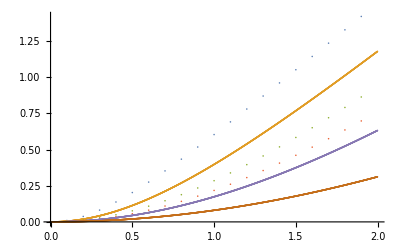

```mathematica
ListPlot[{onePercentScale,twoPercentScale,threePercentScale,fourPercentScale,fivePercentScale,tenPercentScale},PlotRange->All]
```

```mathematica
Evaluate@Fit[twoPercentScale,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x]
Evaluate@Fit[fivePercentScale,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x]
Evaluate@Fit[tenPercentScale,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x]
```

-5.04976×10^-6+0.000284069 x+0.476354 x^2+0.0217614 x^3-0.1822 x^4+0.0932556 x^5-0.00108431 x^6-0.0165341 x^7+0.00631847 x^8-0.000784049 x^9

1.29704×10^-8-7.28467×10^-7 x+0.18051 x^2-0.0000578046 x^3-0.00702489 x^4-0.000315041 x^5+0.000885043 x^6-0.000210604 x^7+0.000011794 x^8+1.22132×10^-6 x^9

3.29718×10^-12-1.50686×10^-10 x+0.081 x^2-4.63808×10^-9 x^3-0.000801902 x^4+4.1619×10^-8 x^5+0.0000143934 x^6+1.35911×10^-7 x^7-4.26291×10^-7 x^8+4.15467×10^-8 x^9

```mathematica
f2[x_]:=Evaluate@Fit[twoPercentScale,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x]
f5[x_]:=Evaluate@Fit[fivePercentScale,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x]
f10[x_]:=Evaluate@Fit[tenPercentScale,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9},x]
```

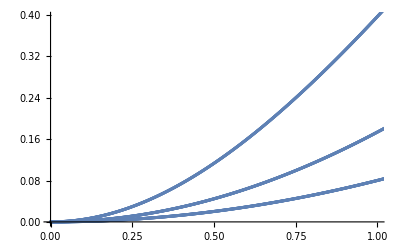

```mathematica
Show[{Plot[f2[x],{x,0,1}],ListPlot[{twoPercentScale}],Plot[f5[x],{x,0,1}],ListPlot[{fivePercentScale}],Plot[f10[x],{x,0,1}],ListPlot[{tenPercentScale}]}]
```

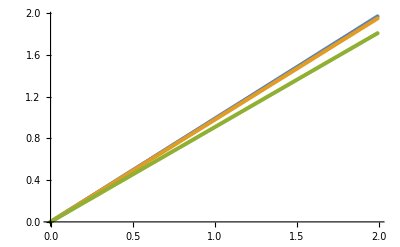

```mathematica
onePercentScaleBound=With[{x=1},Table[{100*i,100*i/(1+x/100)},{i,0.000001,0.02,0.0001}]];
twoPercentScaleBound=With[{x=2},Table[{100*i,100*i/(1+x/100)},{i,0.000001,0.02,0.0001}]];
threePercentScaleBound=With[{x=3},Table[{100*i,100*i/(1+x/100)},{i,0.000001,0.02,0.0001}]];
fourPercentScaleBound=With[{x=4},Table[{100*i,100*i/(1+x/100)},{i,0.000001,0.02,0.0001}]];
fivePercentScaleBound=With[{x=5},Table[{100*i,100*i/(1+x/100)},{i,0.000001,0.02,0.0001}]];
tenPercentScaleBound=With[{x=10},Table[{100*i,100*i/(1+x/100)},{i,0.000001,0.02,0.0001}]];
ListPlot@{onePercentScaleBound,twoPercentScaleBound,tenPercentScaleBound}
```

```mathematica
,
```

{1./(1+x/100),1.6/(1+x/100),2.2/(1+x/100),2.8/(1+x/100)}

```mathematica
Evaluate@Fit[twoPercentScaleBound,{1,x,x^2,x^3,x^4,x^5},x]
Evaluate@Fit[fivePercentScaleBound,{1,x,x^2,x^3,x^4,x^5},x]
Evaluate@Fit[tenPercentScaleBound,{1,x,x^2,x^3,x^4,x^5},x]
```

1.62066×10^-16+0.980392 x+9.73815×10^-15 x^2-1.17489×10^-14 x^3+6.21503×10^-15 x^4-1.22188×10^-15 x^5

8.10329×10^-17+0.952381 x+7.66303×10^-15 x^2-9.35337×10^-15 x^3+5.00639×10^-15 x^4-9.92502×10^-16 x^5

3.24131×10^-16+0.909091 x+1.03781×10^-14 x^2-1.23163×10^-14 x^3+6.26955×10^-15 x^4-1.18928×10^-15 x^5

```mathematica
f2b[x_]:=Evaluate@Fit[twoPercentScaleBound,{1,x,x^2,x^3,x^4,x^5},x]
f5b[x_]:=Evaluate@Fit[fivePercentScaleBound,{1,x,x^2,x^3,x^4,x^5},x]
f10b[x_]:=Evaluate@Fit[tenPercentScaleBound,{1,x,x^2,x^3,x^4,x^5},x]
```